## Base functions

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini_List]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,tst,input=inter},
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
If[!AllTrue[#≤ top&/@tst,#&],
kill=#->0&/@(Position[tst,x_/;x>top]//Flatten);
input=input/.kill;
For[out=ConstantArray[0,n];i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
];
(*Print["\tresult is ",tst];*)
tst
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

## Triangle

#### No lights - all marbles @ node 1

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{1,1,1}]
```

{{1,{2,3}},{1,{1,3}},{1,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[tri,ω,ϕ,30000,2];
```

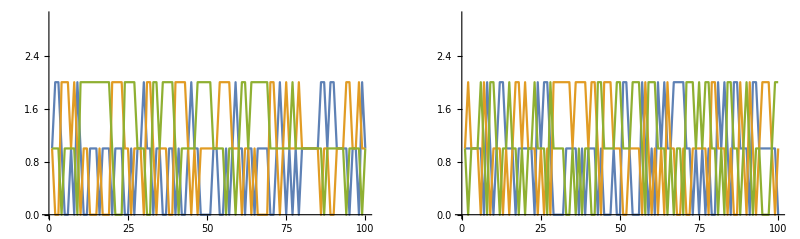

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

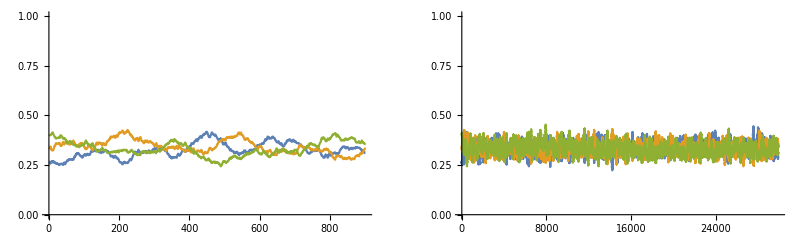

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

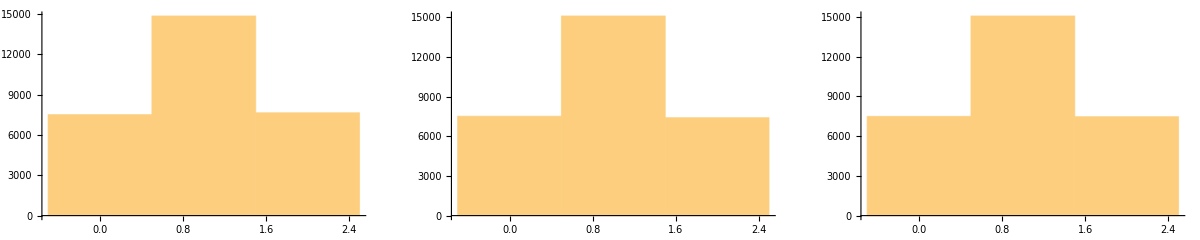

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}];
```

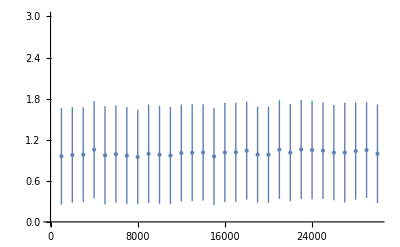

```mathematica
ListPlot[%,PlotRange->{0,3}]
```

## Line

#### No lights - all marbles @ node 1

```mathematica
line=graphToNet[Graph[{1<->2,2<->3}],{1,1,1}]
```

{{1,{2}},{1,{1,3}},{1,{2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[line,ω,ϕ,30000,2];
```

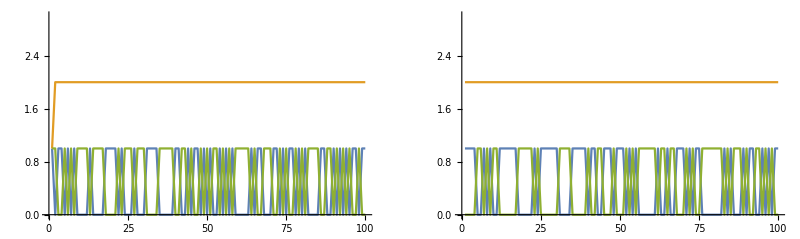

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

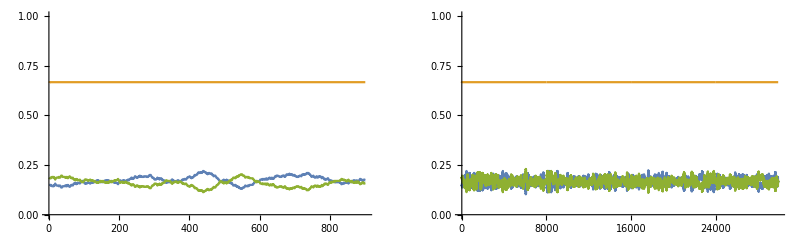

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

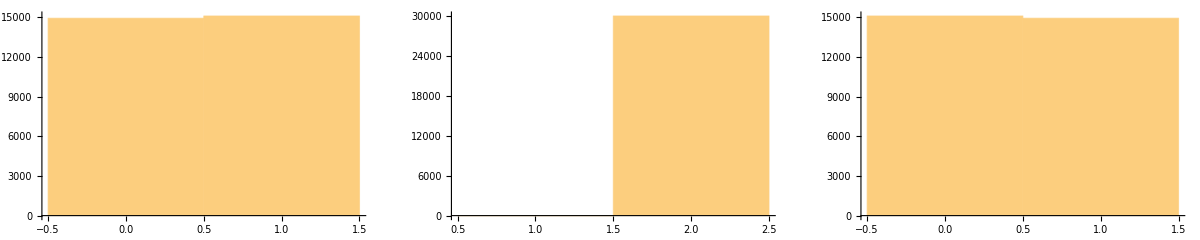

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
devs={Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,2]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,2]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,3]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,3]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]};
```

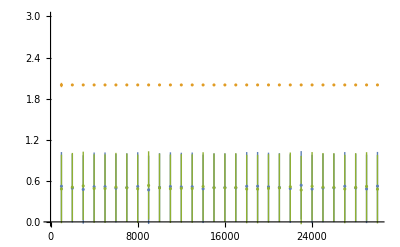

```mathematica
ListPlot[devs,PlotRange->{0,3}]
```

## Long line

#### No lights - all marbles @ node 1

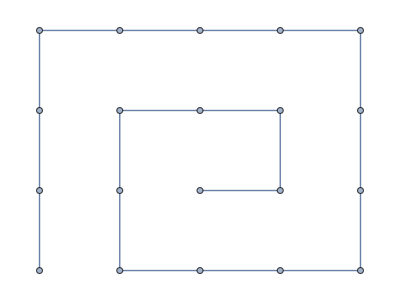

```mathematica
PathGraph[Range[20]]
```

```mathematica
line=graphToNet[PathGraph[Range[20]],ConstantArray[1,20]]
```

{{1,{2}},{1,{1,3}},{1,{2,4}},{1,{3,5}},{1,{4,6}},{1,{5,7}},{1,{6,8}},{1,{7,9}},{1,{8,10}},{1,{9,11}},{1,{10,12}},{1,{11,13}},{1,{12,14}},{1,{13,15}},{1,{14,16}},{1,{15,17}},{1,{16,18}},{1,{17,19}},{1,{18,20}},{1,{19}}}

```mathematica
ω=Table[0,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,Length[line]},{j,Length[line]}];
marbles=netEvolve[line,ω,ϕ,30000,10];
```

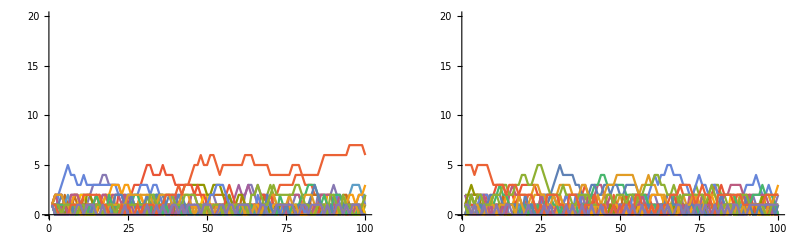

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[line]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[line]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[line]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[line]}],PlotRange->{0,1}]}}]
```

-Graphics-

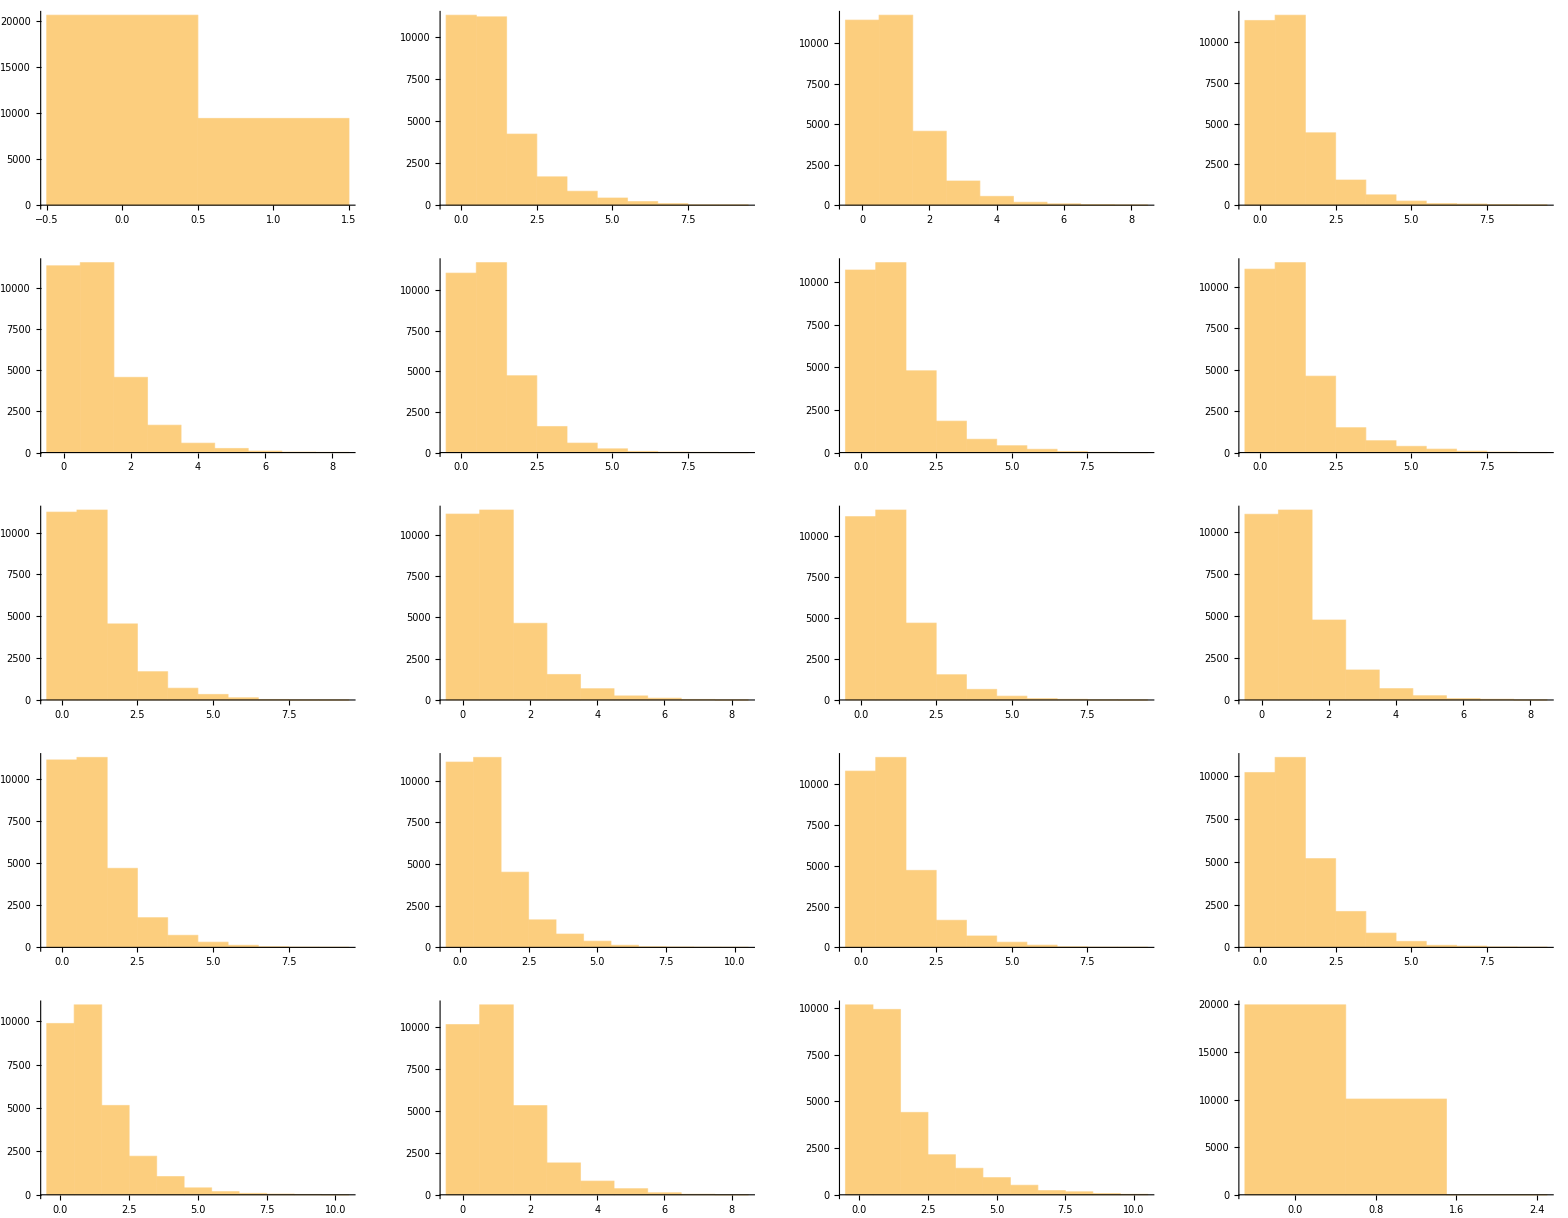

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]],10],{i,Length[line]}],4]]
```

```mathematica
.
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[line]}];
```

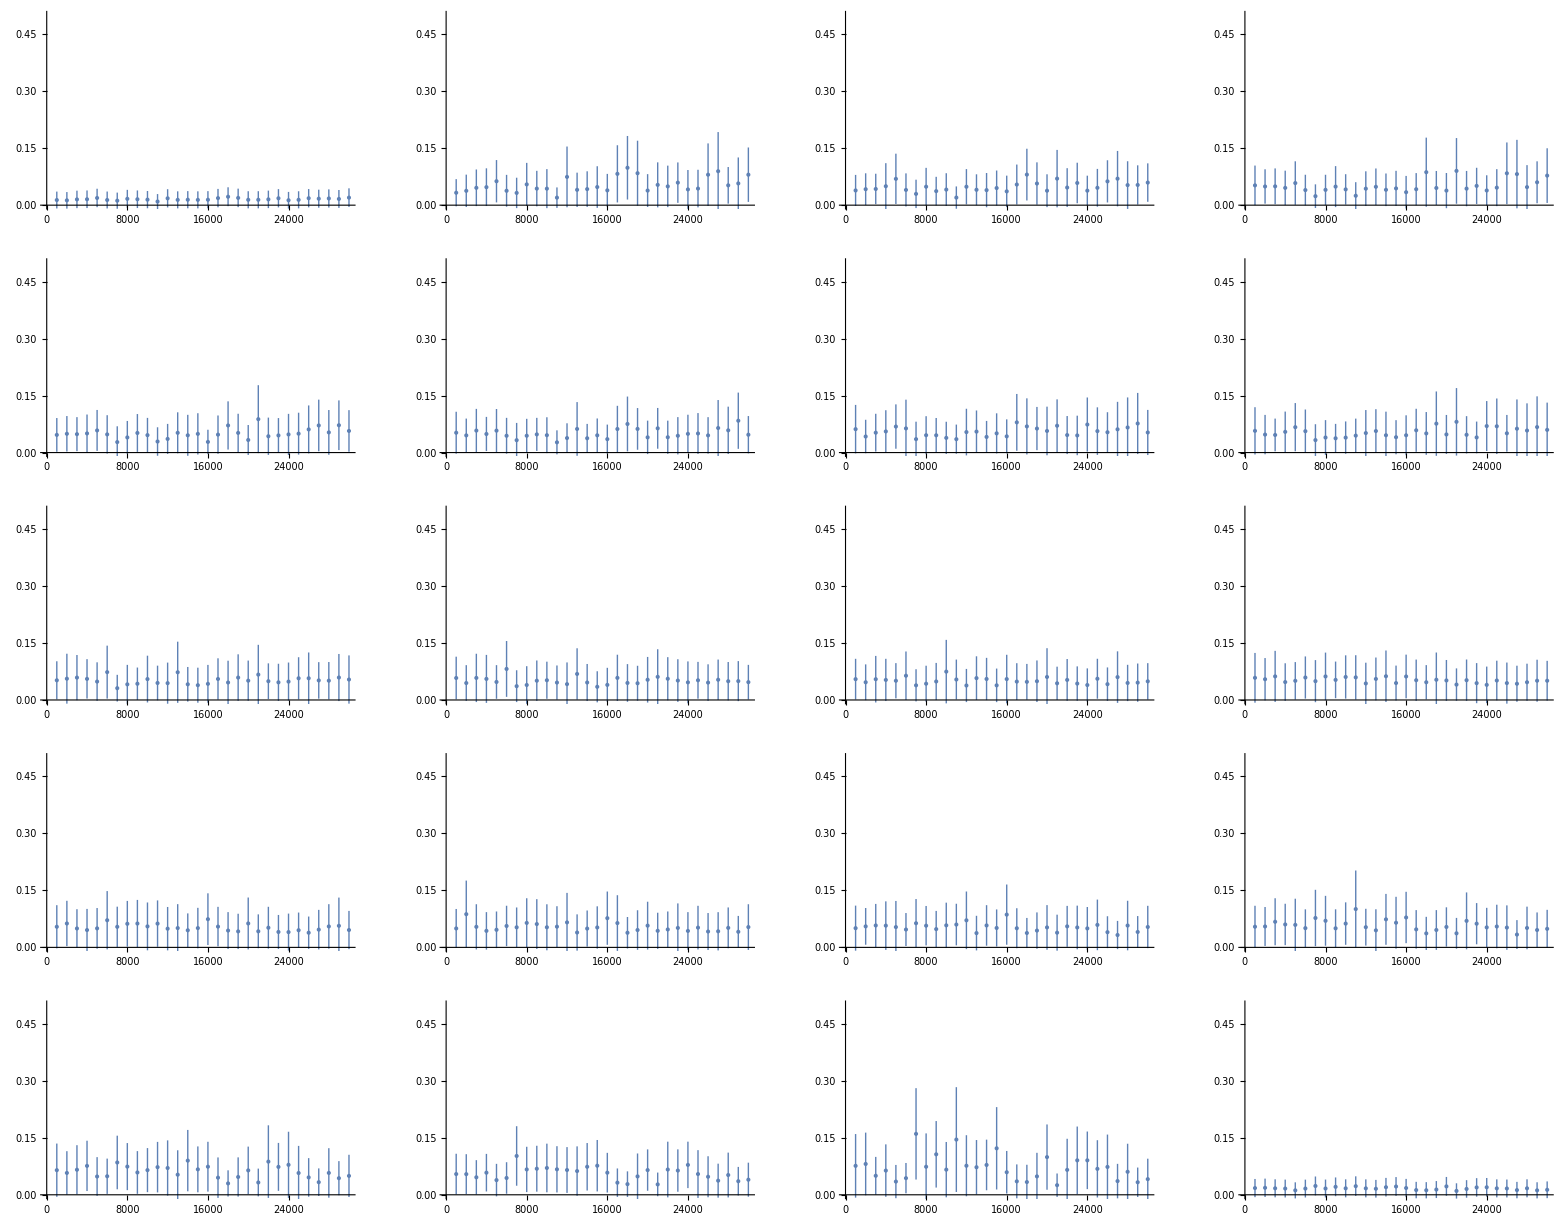

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Long cicle

#### No lights - all marbles @ node 1

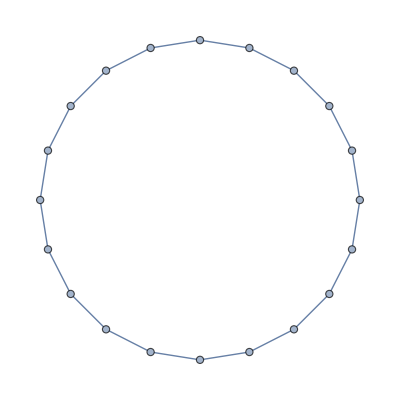

```mathematica
EdgeAdd[PathGraph[Range[20]],20<->1]
```

```mathematica
cicle=graphToNet[EdgeAdd[PathGraph[Range[20]],20<->1],ConstantArray[1,20]]
```

{{1,{2,20}},{1,{1,3}},{1,{2,4}},{1,{3,5}},{1,{4,6}},{1,{5,7}},{1,{6,8}},{1,{7,9}},{1,{8,10}},{1,{9,11}},{1,{10,12}},{1,{11,13}},{1,{12,14}},{1,{13,15}},{1,{14,16}},{1,{15,17}},{1,{16,18}},{1,{17,19}},{1,{18,20}},{1,{1,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[cicle,ω,ϕ,30000,5];
```

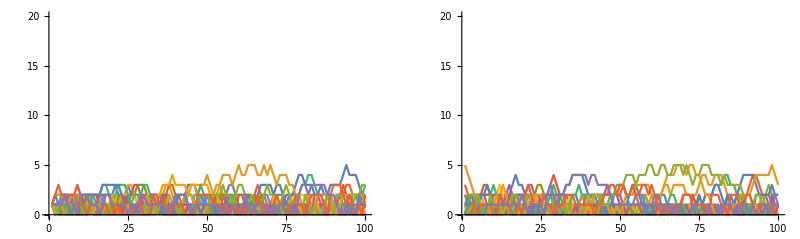

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[cicle]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[cicle]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[cicle]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[cicle]}],PlotRange->{0,1}]}}]
```

-Graphics-

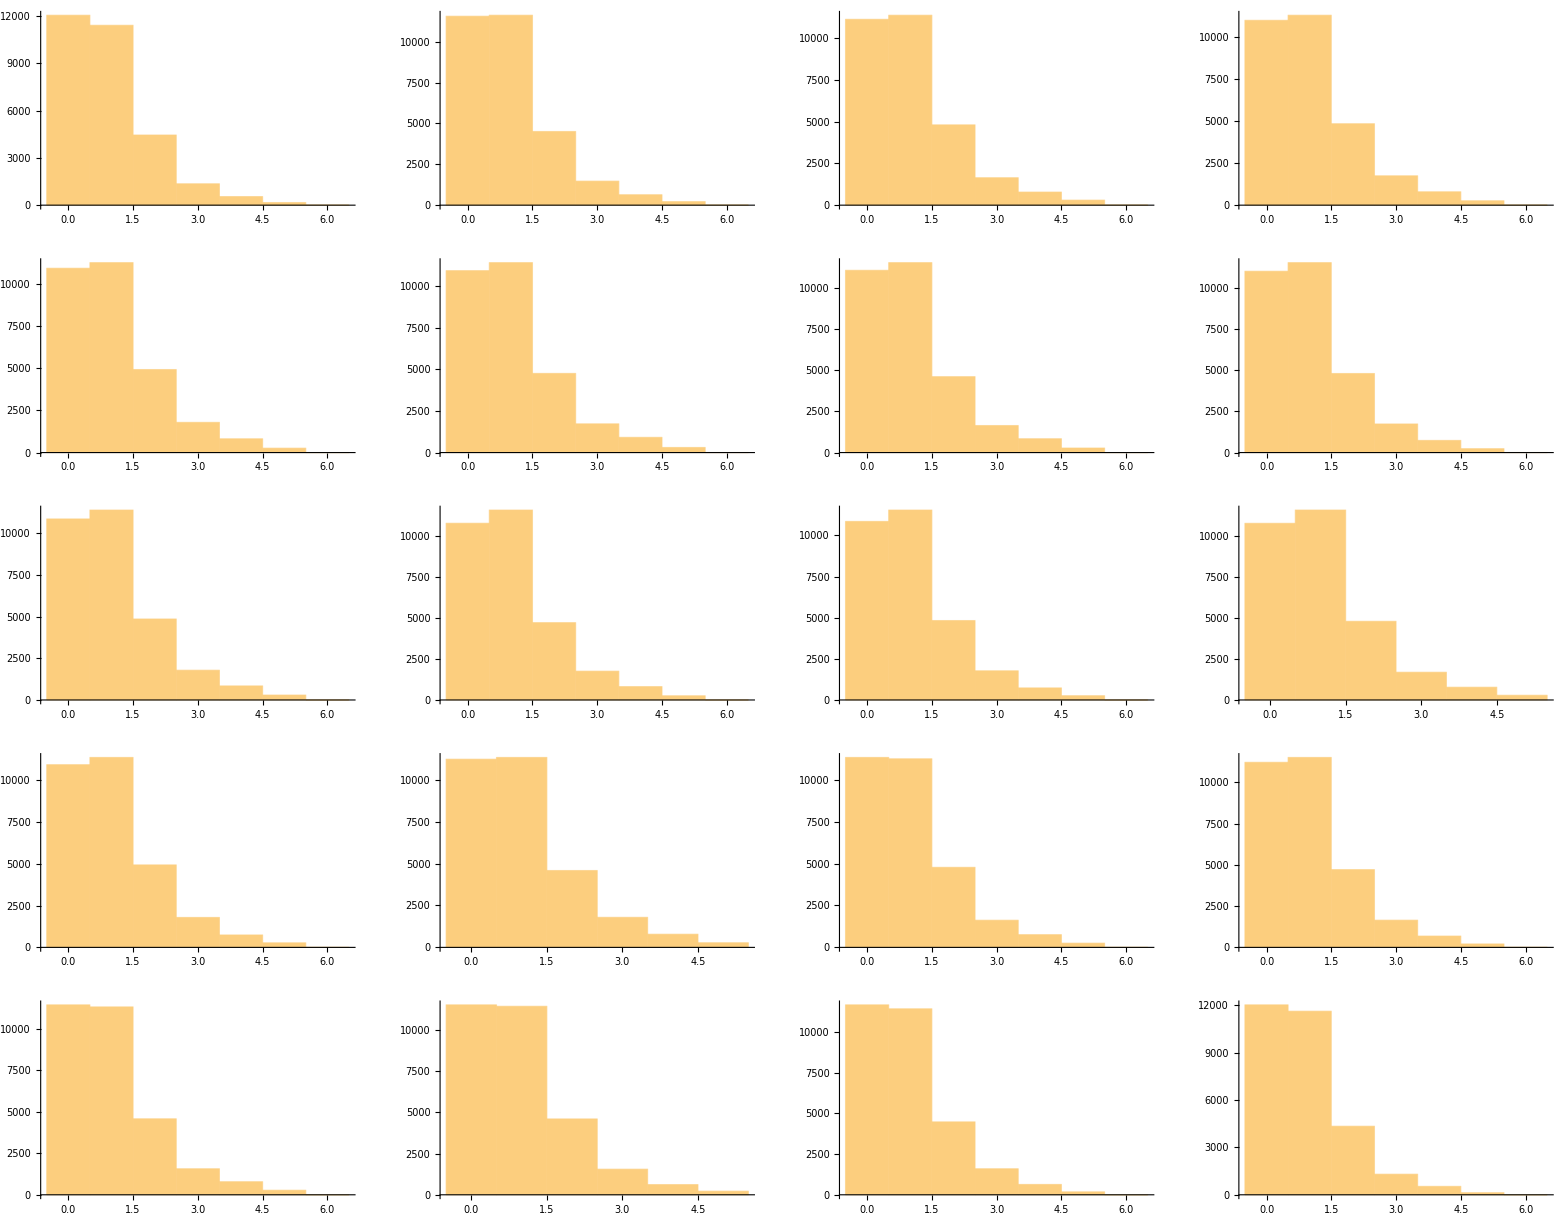

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]],5],{i,Length[cicle]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[cicle]}];
```

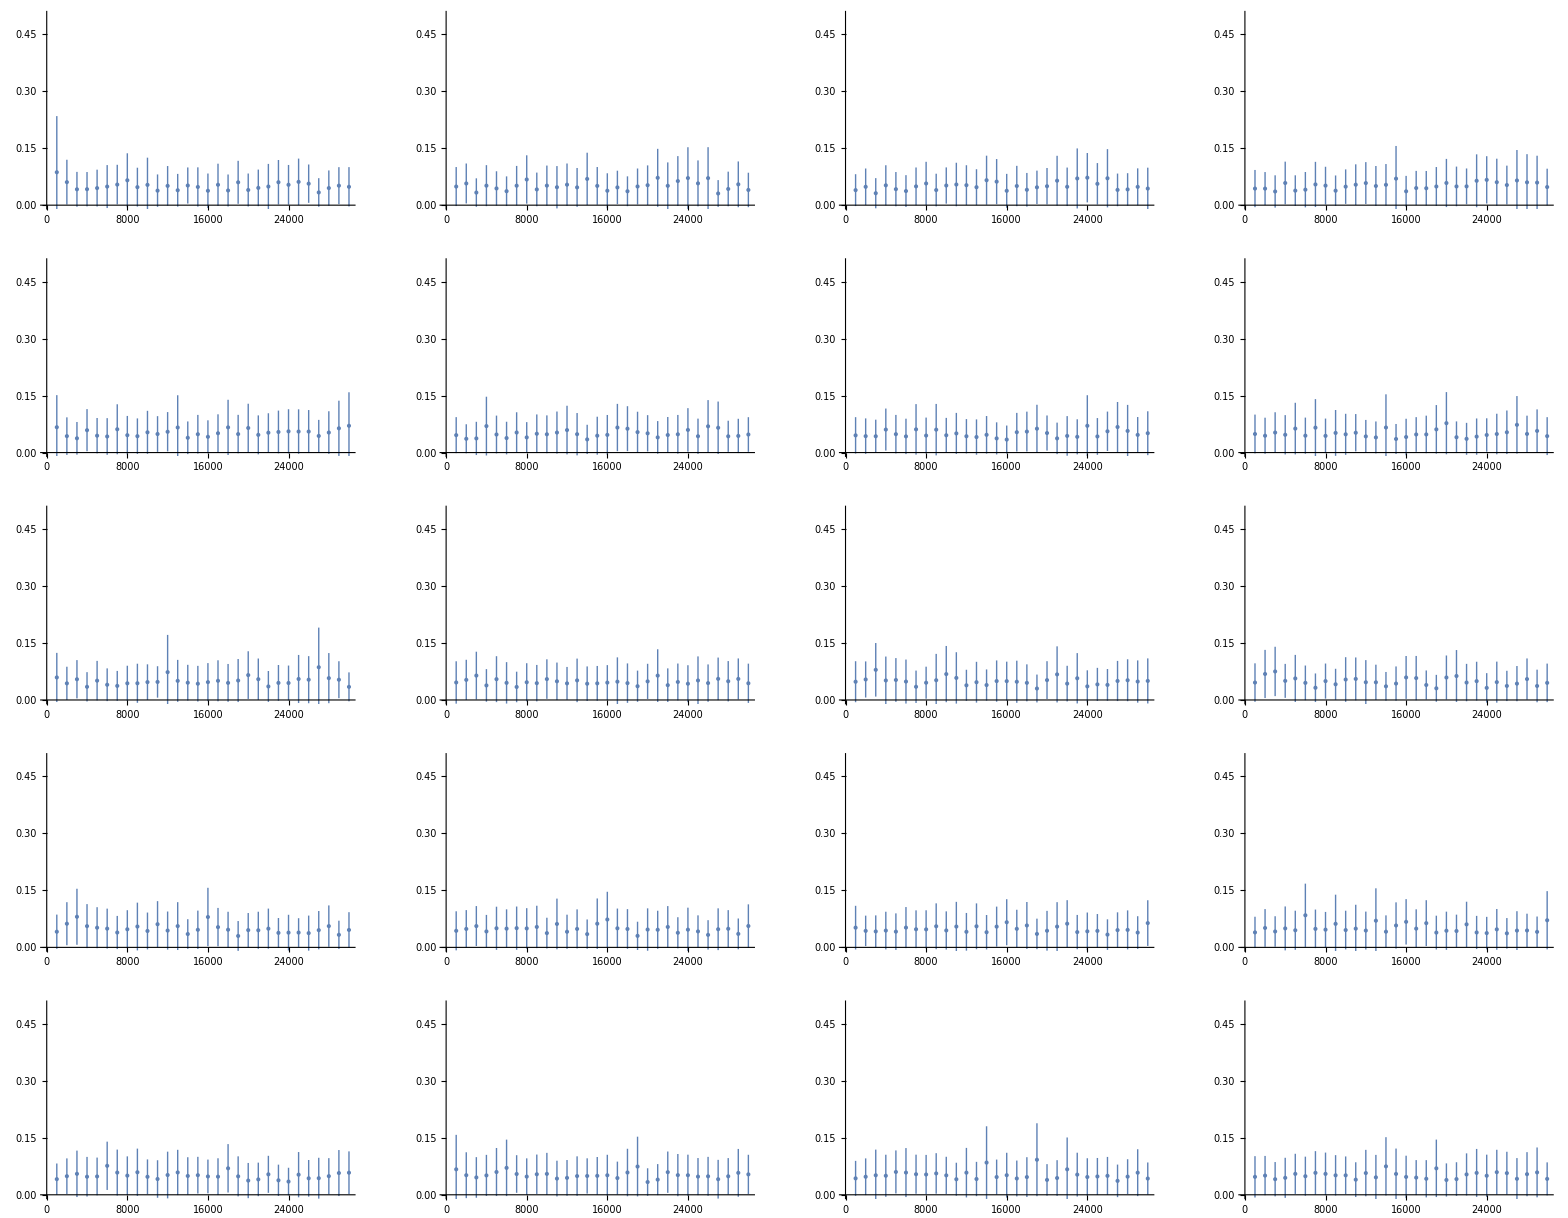

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Scale free

#### No lights - all marbles @ node 1

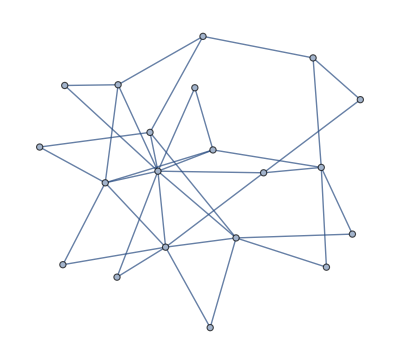

```mathematica
gr=RandomGraph[BarabasiAlbertGraphDistribution[20,2]]
```

```mathematica
VertexDegree[gr]
```

{7,6,10,6,2,4,4,5,4,4,3,2,2,2,2,2,2,2,3,2}

```mathematica
scalefree=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{2,3,4,5,6,17,18}},{1,{1,3,7,9,16,18}},{1,{1,2,4,6,7,9,10,13,14,17}},{1,{1,3,5,10,12,15}},{1,{1,4}},{1,{1,3,8,20}},{1,{2,3,8,13}},{1,{6,7,12,15,19}},{1,{2,3,11,14}},{1,{3,4,11,16}},{1,{9,10,19}},{1,{4,8}},{1,{3,7}},{1,{3,9}},{1,{4,8}},{1,{2,10}},{1,{1,3}},{1,{1,2}},{1,{8,11,20}},{1,{6,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[scalefree,ω,ϕ,30000,5];
```

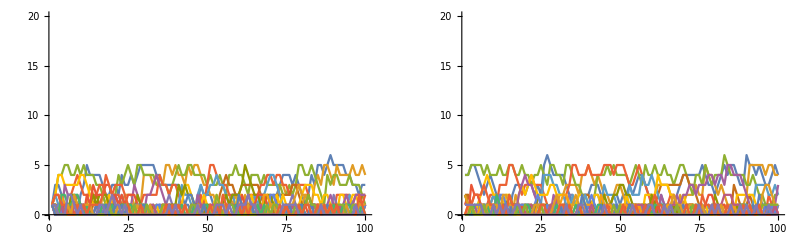

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[scalefree]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[scalefree]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[scalefree]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[scalefree]}],PlotRange->{0,1}]}}]
```

-Graphics-

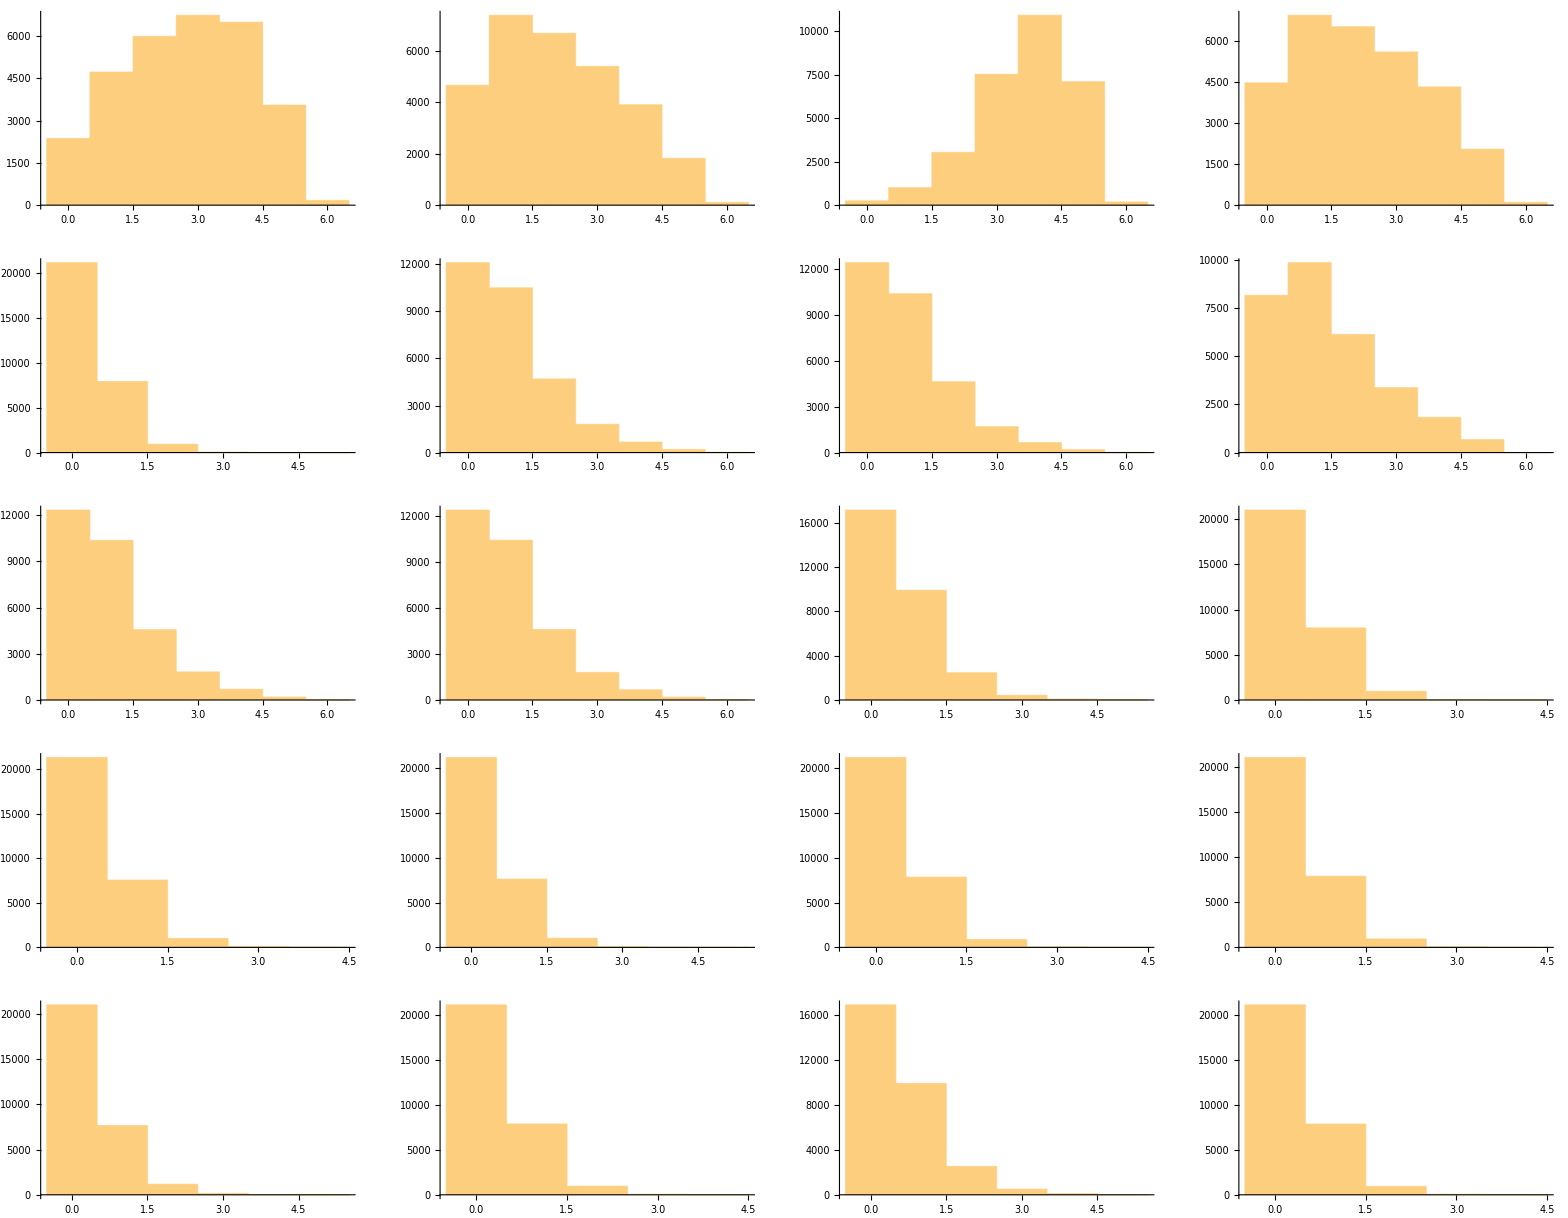

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]],5],{i,Length[scalefree]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[scalefree]}];
```

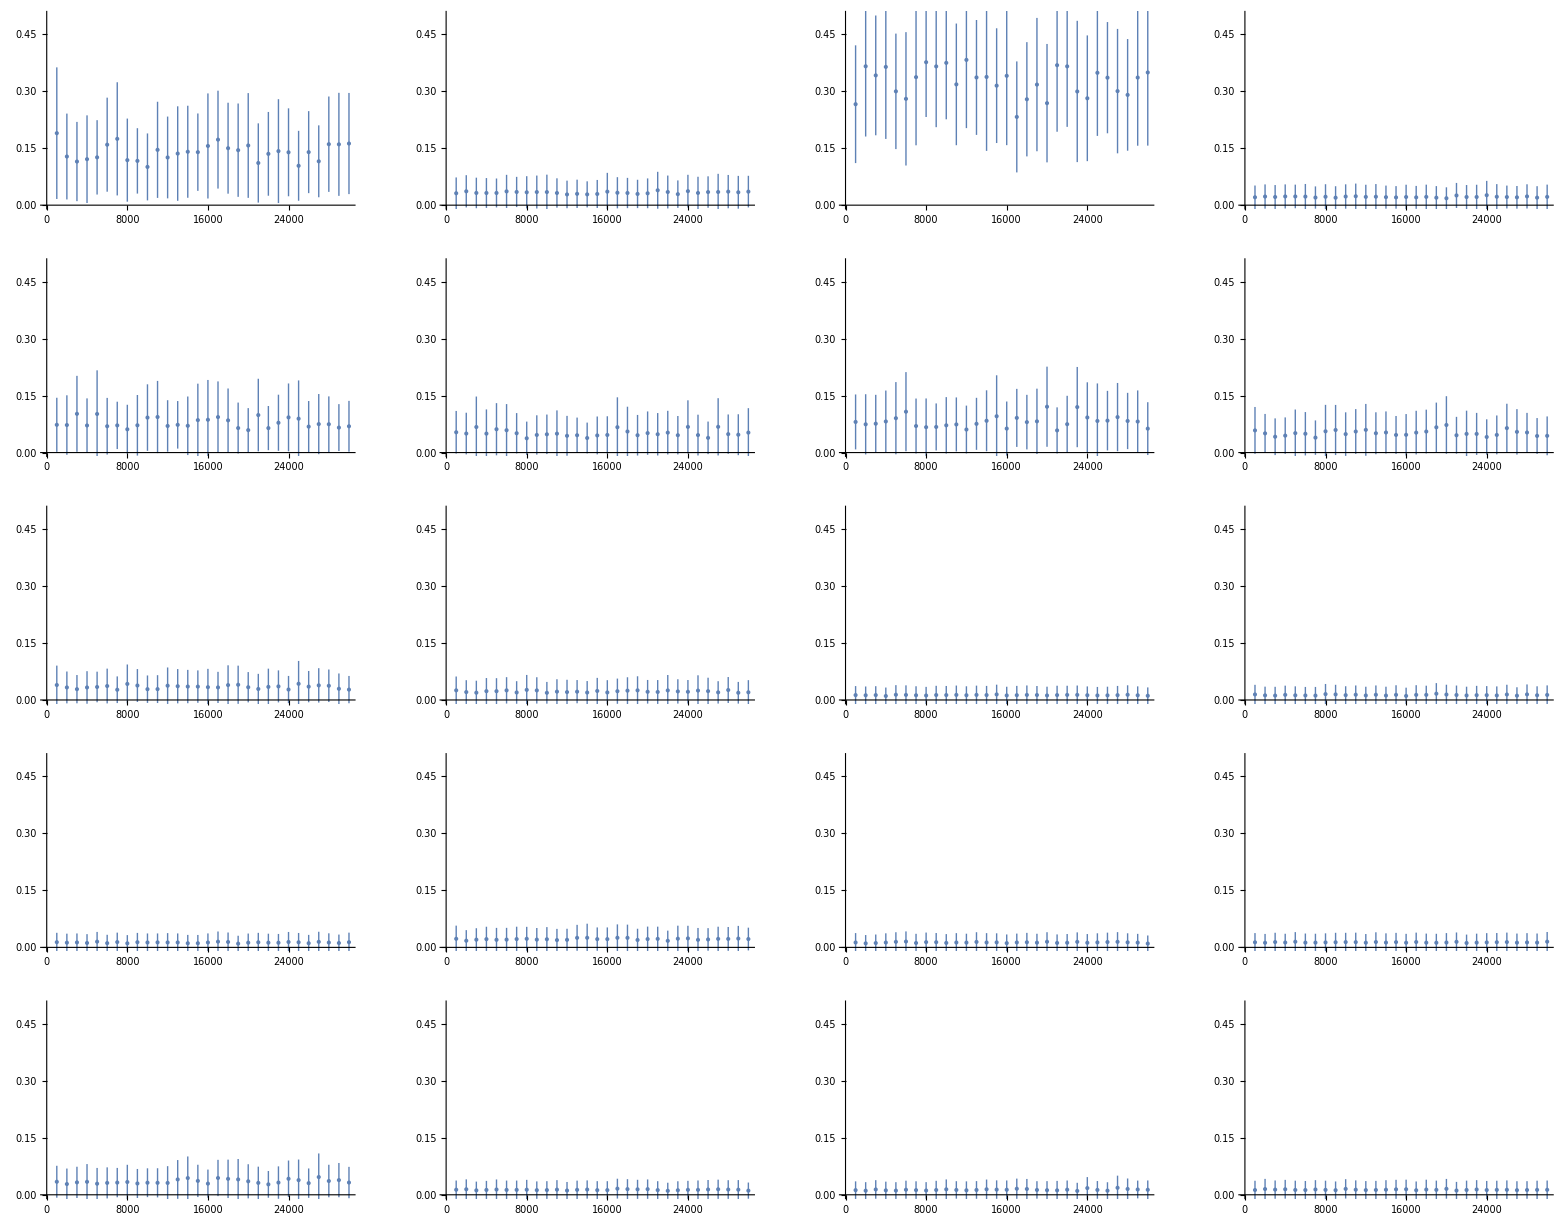

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Small world

#### No lights - all marbles @ node 1

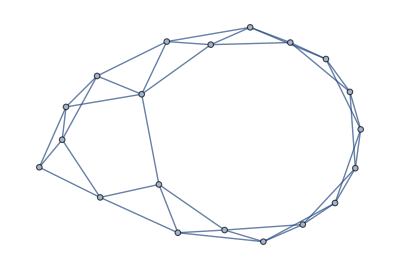

```mathematica
gr=RandomGraph[WattsStrogatzGraphDistribution[20,0.05]]
```

```mathematica
VertexDegree[gr]
```

{4,4,4,4,4,3,4,4,4,5,4,4,4,4,4,4,4,4,4,4}

```mathematica
smallworld=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{2,3,19,20}},{1,{1,3,4,20}},{1,{1,2,4,5}},{1,{2,3,5,10}},{1,{3,4,6,7}},{1,{5,7,8}},{1,{5,6,8,9}},{1,{6,7,9,10}},{1,{7,8,10,11}},{1,{4,8,9,11,12}},{1,{9,10,12,13}},{1,{10,11,13,14}},{1,{11,12,14,15}},{1,{12,13,15,16}},{1,{13,14,16,17}},{1,{14,15,17,18}},{1,{15,16,18,19}},{1,{16,17,19,20}},{1,{1,17,18,20}},{1,{1,2,18,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[smallworld,ω,ϕ,30000,5];
```

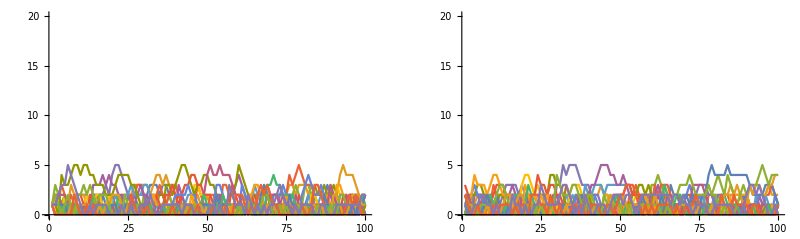

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[smallworld]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[smallworld]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[smallworld]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[smallworld]}],PlotRange->{0,1}]}}]
```

-Graphics-

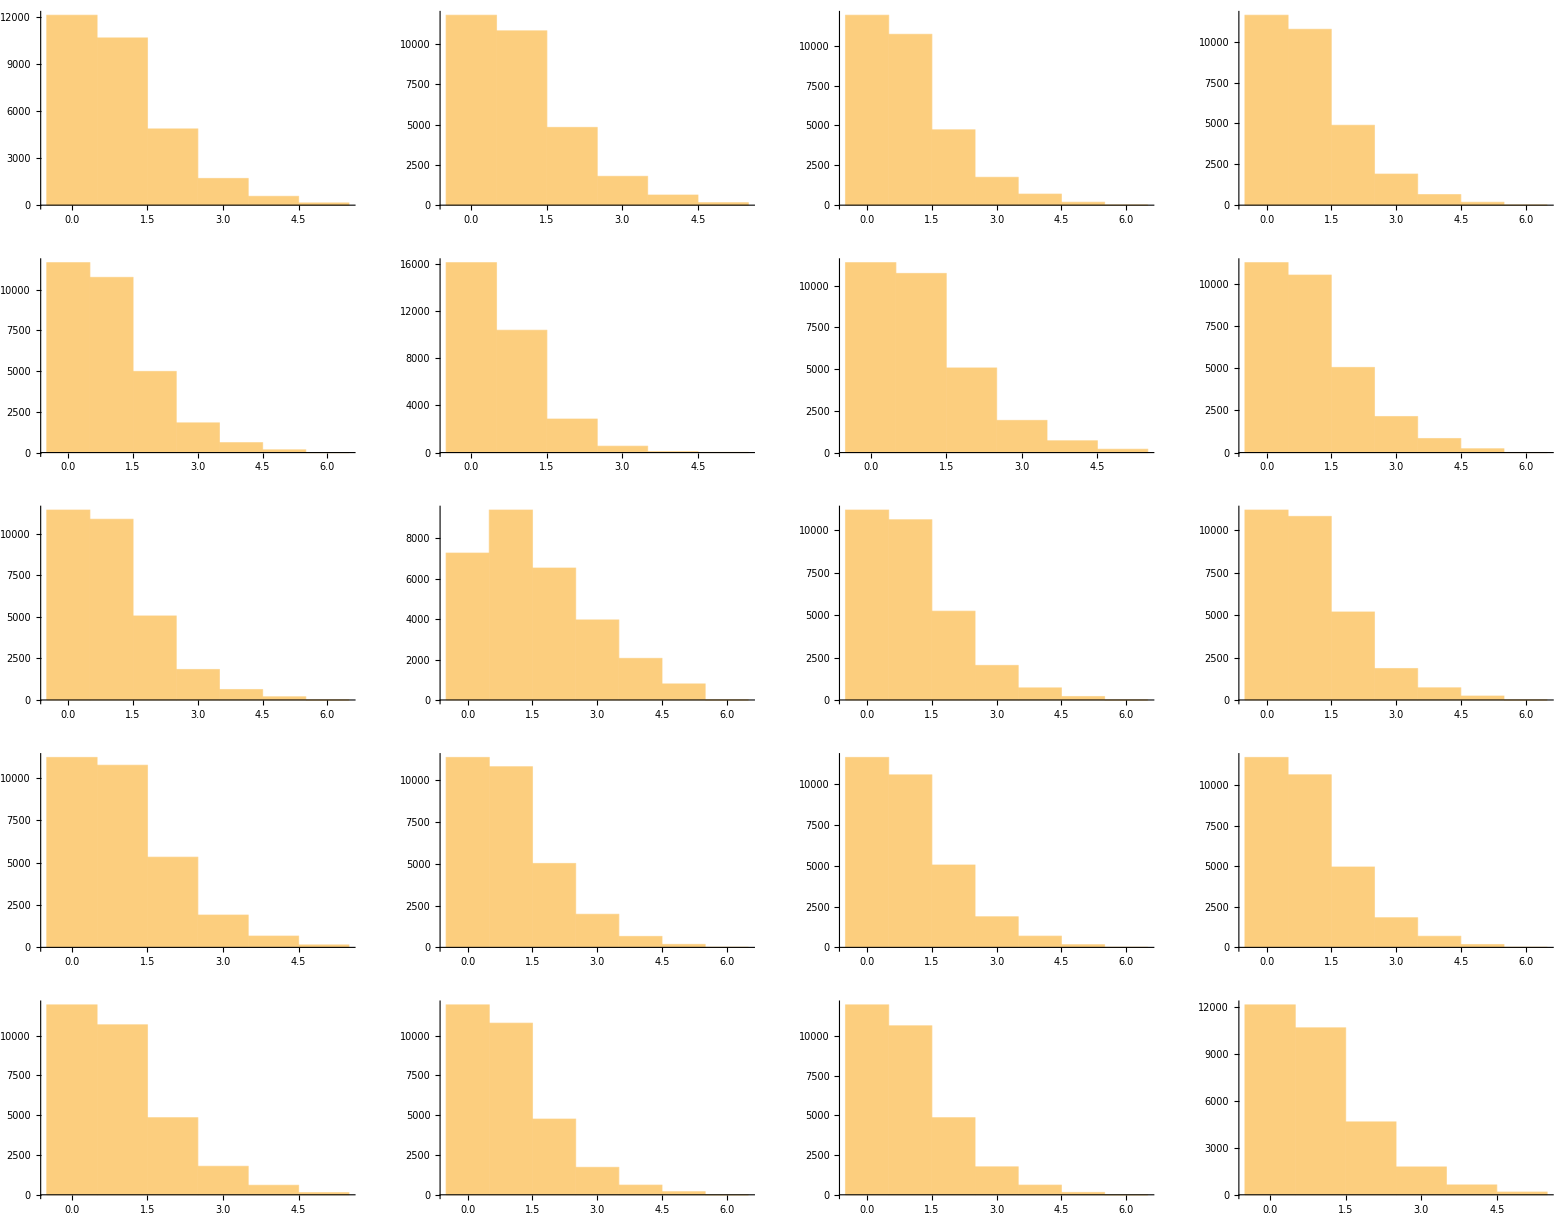

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]],5],{i,Length[smallworld]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[smallworld]}];
```

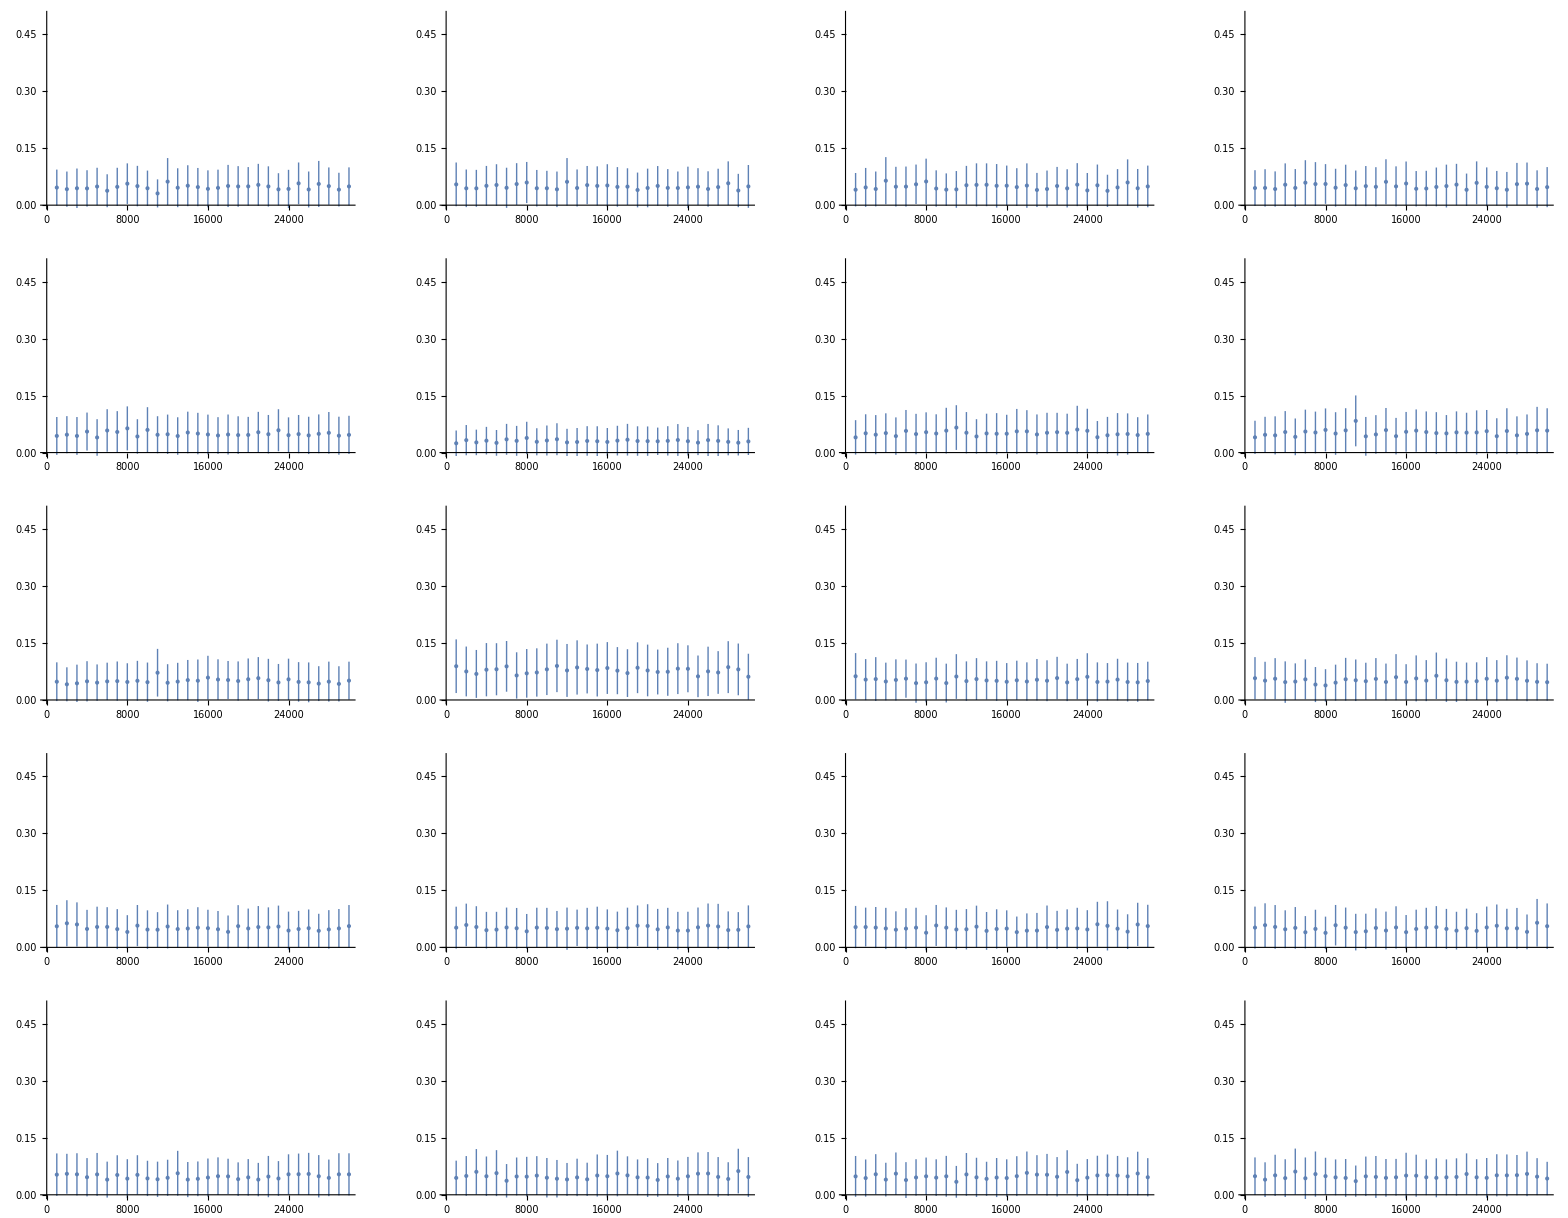

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Random

#### No lights - all marbles @ node 1

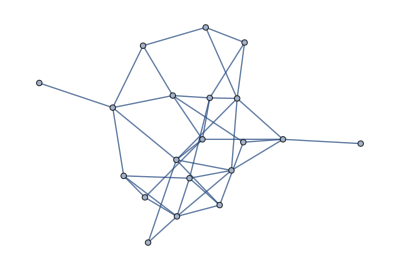

```mathematica
gr=RandomGraph[{20, 40}]
```

```mathematica
VertexDegree[gr]
```

{5,5,2,3,5,6,5,6,3,3,5,5,5,1,6,1,4,3,4,3}

```mathematica
random=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{6,13,16,18,19}},{1,{5,6,10,12,13}},{1,{6,8}},{1,{12,13,17}},{1,{2,11,13,15,20}},{1,{1,2,3,7,15,17}},{1,{6,8,11,12,15}},{1,{3,7,10,11,17,19}},{1,{15,18,20}},{1,{2,8,19}},{1,{5,7,8,17,19}},{1,{2,4,7,14,15}},{1,{1,2,4,5,18}},{1,{12}},{1,{5,6,7,9,12,20}},{1,{1}},{1,{4,6,8,11}},{1,{1,9,13}},{1,{1,8,10,11}},{1,{5,9,15}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[random,ω,ϕ,30000,5];
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[random]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[random]}],PlotRange->{0,20}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[random]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[random]}],PlotRange->{0,1}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]],6],{i,Length[random]}],4]]
```

-Graphics-

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[random]}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

-Graphics-

## Complete network

11 nodes, al with degree 10

```mathematica
CompleteGraph[11]
```

-Graphics-

#### No lights - all marbles @ node 1

```mathematica
complete=graphToNet[CompleteGraph[11],ConstantArray[1,11]]
```

{{1,{2,3,4,5,6,7,8,9,10,11}},{1,{1,3,4,5,6,7,8,9,10,11}},{1,{1,2,4,5,6,7,8,9,10,11}},{1,{1,2,3,5,6,7,8,9,10,11}},{1,{1,2,3,4,6,7,8,9,10,11}},{1,{1,2,3,4,5,7,8,9,10,11}},{1,{1,2,3,4,5,6,8,9,10,11}},{1,{1,2,3,4,5,6,7,9,10,11}},{1,{1,2,3,4,5,6,7,8,10,11}},{1,{1,2,3,4,5,6,7,8,9,11}},{1,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,300,5];
```

```mathematica
marbles//Short
```

{{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,0,2,2,0,1,1},{0,1,1,1,0,0,2,3,3,0,0},«295»,{2,3,0,0,2,0,0,1,1,1,1},{2,3,0,1,2,0,0,1,2,0,0},{2,3,0,0,2,1,0,0,2,1,0}}

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
complete=graphToNet[CompleteGraph[11],ConstantArray[100,11]]
```

{{100,{2,3,4,5,6,7,8,9,10,11}},{100,{1,3,4,5,6,7,8,9,10,11}},{100,{1,2,4,5,6,7,8,9,10,11}},{100,{1,2,3,5,6,7,8,9,10,11}},{100,{1,2,3,4,6,7,8,9,10,11}},{100,{1,2,3,4,5,7,8,9,10,11}},{100,{1,2,3,4,5,6,8,9,10,11}},{100,{1,2,3,4,5,6,7,9,10,11}},{100,{1,2,3,4,5,6,7,8,10,11}},{100,{1,2,3,4,5,6,7,8,9,11}},{100,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two dense networks joined by a bridge

```mathematica
bridgegrapgh=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,4<->5,6<->7,7<->8,7<->9,7<->10,7<->11,8<->9,8<->10,8<->11,9<->10,9<->11,10<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - all marbles in few nodes

```mathematica
bridge=graphToNet[bridgegrapgh,{0,5,0,0,0,5,5,0,0,0,0}]
```

{{0,{2,3,4,5}},{5,{1,3,4,5,6}},{0,{1,2,4,5}},{0,{1,2,3,5}},{0,{1,2,3,4}},{5,{2,7}},{5,{6,8,9,10,11}},{0,{7,9,10,11}},{0,{7,8,10,11}},{0,{7,8,9,11}},{0,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000,5];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/15,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
bridge=graphToNet[bridgegrapgh,ConstantArray[2,11]]
```

{{2,{2,3,4,5}},{2,{1,3,4,5,6}},{2,{1,2,4,5}},{2,{1,2,3,5}},{2,{1,2,3,4}},{2,{2,7}},{2,{6,8,9,10,11}},{2,{7,9,10,11}},{2,{7,8,10,11}},{2,{7,8,9,11}},{2,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000,5];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(2 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two sparse networks joined by a bridge

```mathematica
sparsebridgegraph=Graph[{1<->5,2<->5,3<->5,4<->5,5<->6,6<->7,7<->8,7<->9,7<->10,7<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - all marbles @ node 1

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,{100,1}]
```

{{100,{2}},{0,{1,3,4,5,6}},{0,{2}},{0,{2}},{0,{2}},{0,{2,7}},{0,{6,8,9,10,11}},{0,{7}},{0,{7}},{0,{7}},{0,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,ConstantArray[100,11]]
```

{{100,{2}},{100,{1,3,4,5,6}},{100,{2}},{100,{2}},{100,{2}},{100,{2,7}},{100,{6,8,9,10,11}},{100,{7}},{100,{7}},{100,{7}},{100,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100  11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Tope al número de paquetes que puede haber en un nodo. La regla nueva es, cada nodo tiene una capacidad máxima, en cada tick recibe paquetes si y solo si su capacidad máxima no es superada, si fuera superada no recibe ningún paquete (el número de paquetes debería bajar o permanecer constante)

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i,places,tst,input=inter},
For[i=1,i≤n,i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
While[!AllTrue[#≤ top&/@tst,#&],
places=Flatten[Position[tst,x_/;x>top]];
input=Flatten[input/.(Rule[#,0]&/@places)];
(*Print["i is ",Length[input]];
Print["input is ",input];*)
For[i=1;out=ConstantArray[0,n],i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;];
];
(*Print["\t\tout after check is ",out];*)
tst=marbles[[-1]]+out;
];
(*Print["\tresult is ",tst];*)
tst
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

```mathematica
J[ts_List]:=Mean[Total/@Abs/@Table[ts[[i+1]]-ts[[i]],{i,Length[ts]-1}]]
```

## Calcular el J en todos los casos (fracción de paquetes que se movieron). J Vs. máximo de paquetes.

## Triangle

#### No lights - all nodes with same number of marbles

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{1,1,1}]
```

{{1,{2,3}},{1,{1,3}},{1,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=Table[netEvolve[tri,ω,ϕ,300,j],{j,Length[tri]+2}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Line

#### No lights - all nodes with same number of marbles

```mathematica
line=graphToNet[Graph[{1<->2,2<->3}],{1,1,1}]
```

{{1,{2}},{1,{1,3}},{1,{2}}}

```mathematica
ω=Table[0,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,Length[line]},{j,Length[line]}];
marbles=Table[netEvolve[line,ω,ϕ,300,j],{j,Length[line]+5}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Long line

#### No lights - all nodes with same number of marbles

```mathematica
PathGraph[Range[20]]
```

-Graphics-

```mathematica
line=graphToNet[PathGraph[Range[20]],ConstantArray[1,20]]
```

{{1,{2}},{1,{1,3}},{1,{2,4}},{1,{3,5}},{1,{4,6}},{1,{5,7}},{1,{6,8}},{1,{7,9}},{1,{8,10}},{1,{9,11}},{1,{10,12}},{1,{11,13}},{1,{12,14}},{1,{13,15}},{1,{14,16}},{1,{15,17}},{1,{16,18}},{1,{17,19}},{1,{18,20}},{1,{19}}}

```mathematica
ω=Table[0,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,Length[line]},{j,Length[line]}];
```

```mathematica
marbles=Table[netEvolve[line,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Long cicle

#### No lights - all nodes with same number of marbles

```mathematica
EdgeAdd[PathGraph[Range[20]],20<->1]
```

-Graphics-

```mathematica
cicle=graphToNet[EdgeAdd[PathGraph[Range[20]],20<->1],ConstantArray[1,20]]
```

{{1,{2,20}},{1,{1,3}},{1,{2,4}},{1,{3,5}},{1,{4,6}},{1,{5,7}},{1,{6,8}},{1,{7,9}},{1,{8,10}},{1,{9,11}},{1,{10,12}},{1,{11,13}},{1,{12,14}},{1,{13,15}},{1,{14,16}},{1,{15,17}},{1,{16,18}},{1,{17,19}},{1,{18,20}},{1,{1,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
```

```mathematica
marbles=Table[netEvolve[cicle,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Scale free

#### No lights - all nodes with same number of marbles

```mathematica
gr=RandomGraph[BarabasiAlbertGraphDistribution[20,2]]
```

-Graphics-

```mathematica
VertexDegree[gr]
```

{7,5,9,6,6,3,3,3,3,2,4,3,5,2,2,2,2,3,2,2}

```mathematica
scalefree=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{2,3,4,5,7,8,13}},{1,{1,3,12,15,19}},{1,{1,2,4,6,7,9,10,12,17}},{1,{1,3,5,6,9,20}},{1,{1,4,8,10,14,16}},{1,{3,4,13}},{1,{1,3,11}},{1,{1,5,11}},{1,{3,4,14}},{1,{3,5}},{1,{7,8,15,18}},{1,{2,3,18}},{1,{1,6,16,17,20}},{1,{5,9}},{1,{2,11}},{1,{5,13}},{1,{3,13}},{1,{11,12,19}},{1,{2,18}},{1,{4,13}}}

```mathematica
ω=Table[0,{i,Length[scalefree]},{j,Length[scalefree]}];
ϕ=Table[0,{i,Length[scalefree]},{j,Length[scalefree]}];
```

```mathematica
marbles=Table[netEvolve[cicle,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Small world

#### No lights - all nodes with same number of marbles

```mathematica
gr=RandomGraph[WattsStrogatzGraphDistribution[20,0.05]]
```

-Graphics-

```mathematica
VertexDegree[gr]
```

{4,4,4,4,4,3,3,5,4,4,3,4,5,4,4,4,4,5,4,4}

```mathematica
smallworld=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{2,3,19,20}},{1,{1,3,4,20}},{1,{1,2,4,5}},{1,{2,3,5,6}},{1,{3,4,13,18}},{1,{4,7,8}},{1,{6,8,9}},{1,{6,7,9,10,12}},{1,{7,8,10,11}},{1,{8,9,11,12}},{1,{9,10,13}},{1,{8,10,13,14}},{1,{5,11,12,14,15}},{1,{12,13,15,16}},{1,{13,14,16,17}},{1,{14,15,17,18}},{1,{15,16,18,19}},{1,{5,16,17,19,20}},{1,{1,17,18,20}},{1,{1,2,18,19}}}

```mathematica
ω=Table[0,{i,Length[smallworld]},{j,Length[smallworld]}];
ϕ=Table[0,{i,Length[smallworld]},{j,Length[smallworld]}];
```

```mathematica
marbles=Table[netEvolve[smallworld,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Random

#### No lights - all nodes with same number of marbles

```mathematica
gr=RandomGraph[{20, 40}]
```

-Graphics-

```mathematica
VertexDegree[gr]
```

{2,5,2,4,0,3,3,4,9,6,3,6,4,4,6,6,4,2,3,4}

```mathematica
random=graphToNet[gr,ConstantArray[1,20]]
```

{{1,{12,14}},{1,{8,12,17,18,19}},{1,{4,16}},{1,{3,9,12,16}},{1,{}},{1,{9,16,20}},{1,{11,13,14}},{1,{2,10,15,19}},{1,{4,6,10,12,13,14,15,16,20}},{1,{8,9,11,13,17,18}},{1,{7,10,15}},{1,{1,2,4,9,15,17}},{1,{7,9,10,15}},{1,{1,7,9,15}},{1,{8,9,11,12,13,14}},{1,{3,4,6,9,17,20}},{1,{2,10,12,16}},{1,{2,10}},{1,{2,8,20}},{1,{6,9,16,19}}}

```mathematica
ω=Table[0,{i,Length[random]},{j,Length[random]}];
ϕ=Table[0,{i,Length[random]},{j,Length[random]}];
```

```mathematica
marbles=Table[netEvolve[random,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Complete network

11 nodes, al with degree 10

```mathematica
CompleteGraph[11]
```

-Graphics-

#### No lights - all nodes with same number of marbles

```mathematica
complete=graphToNet[CompleteGraph[11],ConstantArray[1,11]]
```

{{1,{2,3,4,5,6,7,8,9,10,11}},{1,{1,3,4,5,6,7,8,9,10,11}},{1,{1,2,4,5,6,7,8,9,10,11}},{1,{1,2,3,5,6,7,8,9,10,11}},{1,{1,2,3,4,6,7,8,9,10,11}},{1,{1,2,3,4,5,7,8,9,10,11}},{1,{1,2,3,4,5,6,8,9,10,11}},{1,{1,2,3,4,5,6,7,9,10,11}},{1,{1,2,3,4,5,6,7,8,10,11}},{1,{1,2,3,4,5,6,7,8,9,11}},{1,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
```

```mathematica
marbles=Table[netEvolve[complete,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Two dense networks joined by a bridge

```mathematica
bridgegrapgh=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,4<->5,6<->7,7<->8,7<->9,7<->10,7<->11,8<->9,8<->10,8<->11,9<->10,9<->11,10<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - all nodes with same number of marbles

```mathematica
bridge=graphToNet[bridgegrapgh,ConstantArray[1,11]]
```

{{1,{2,3,4,5}},{1,{1,3,4,5,6}},{1,{1,2,4,5}},{1,{1,2,3,5}},{1,{1,2,3,4}},{1,{2,7}},{1,{6,8,9,10,11}},{1,{7,9,10,11}},{1,{7,8,10,11}},{1,{7,8,9,11}},{1,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[bridge]},{j,Length[bridge]}];
ϕ=Table[0,{i,Length[bridge]},{j,Length[bridge]}];
```

```mathematica
marbles=Table[netEvolve[bridge,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

## Two sparse networks joined by a bridge

```mathematica
sparsebridgegraph=Graph[{1<->5,2<->5,3<->5,4<->5,5<->6,6<->7,7<->8,7<->9,7<->10,7<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - marbles all over

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,ConstantArray[1,11]]
```

{{1,{2}},{1,{1,3,4,5,6}},{1,{2}},{1,{2}},{1,{2}},{1,{2,7}},{1,{6,8,9,10,11}},{1,{7}},{1,{7}},{1,{7}},{1,{7}}}

```mathematica
ω=Table[0,{i,Length[sparsebridge]},{j,Length[sparsebridge]}];
ϕ=Table[0,{i,Length[sparsebridge]},{j,Length[sparsebridge]}];
```

```mathematica
marbles=Table[netEvolve[sparsebridge,ω,ϕ,200,j],{j,1,20}];
```

```mathematica
ListPlot[J/@marbles,AxesLabel->{"Max #","J"}]
```

-Graphics-

2. Poner todos semáforos iguales, cambiar la fase en pocos y ver qué pasa con el flujo (# de paquetes por periodo), que fases deben tener para no empeorar.